### Let’s take a look at the conditions for A-stability for 2-step methods

#### First, the consistency conditions

```mathematica
orderConditions=And@@Table[Sum[Subscript[α, i] i^(q+ϵ),{i,0,2}]==q Sum[Subscript[β, i] (i)^(q+ϵ-1),{i,0,2}],{q,0,2}]/.{ 0^ϵ->1, 0^(-1+ϵ)->0,ϵ->0}
```

α_0+α_1+α_2==0&&α_1+2 α_2==β_0+β_1+β_2&&α_1+4 α_2==2 (β_1+2 β_2)

```mathematica
BDFLikeOrderConditions=orderConditions/.{Subscript[α, 2]->1}
```

1+α_0+α_1==0&&2+α_1==β_0+β_1+β_2&&4+α_1==2 (β_1+2 β_2)

```mathematica
reducedBDFLikeOrderConditions=Reduce[BDFLikeOrderConditions]//ToRules
```

{β_0→-2+β_1+3 β_2,α_1→-4+2 β_1+4 β_2,α_0→3-2 β_1-4 β_2}

#### We then take the derivations from Lajos on A-stability for 2-step methods

```mathematica
N0=α0 β0+α1 β0+α2 β0+α0 β1+α1 β1+α2 β1+α0 β2+α1 β2+α2 β2;
N2=2 α0 β0-6 α2 β0+2 α1 β1-6 α0 β2+2 α2 β2;
N4=α0 β0-α1 β0+α2 β0-α0 β1+α1 β1-α2 β1+α0 β2-α1 β2+α2 β2;
D0=β0^2+2 β0 β1+β1^2+2 β0 β2+2 β1 β2+β2^2;
D2=2 β0^2+2 β1^2-12 β0 β2+2 β2^2;
D4=β0^2-2 β0 β1+β1^2+2 β0 β2-2 β1 β2+β2^2;
(N0==0&&D0>0&&D4>D2^2/(4 D0)&&N2≥0&&N4≥0&&D2<0)||(N0==0&&D0>0&&D2≥0&&D4≥0&&N2≥0&&N4≥0)||(N0==0&&D2>0&&D0<0&&D4<D2^2/(4 D0)&&N2≤0&&N4≤0)||(N0==0&&D0<0&&D2≤0&&D4≤0&&N2≤0&&N4≤0)||(D0>0&&D4>D2^2/(4 D0)&&N0>0&&N2≥0&&N4≥0&&D2<0)||(D0>0&&D4>D2^2/(4 D0)&&N0>0&&N4≥N2^2/(4 N0)&&D2<0&&N2<0)||(D0>0&&N0>0&&D2≥0&&D4≥0&&N2≥0&&N4≥0)||(D0>0&&N0>0&&D2≥0&&D4≥0&&N4≥N2^2/(4 N0)&&N2<0)||(D2>0&&N2>0&&D0<0&&D4<D2^2/(4 D0)&&N0<0&&N4≤N2^2/(4 N0))||(D2>0&&D0<0&&D4<D2^2/(4 D0)&&N0<0&&N2≤0&&N4≤0)||(N2>0&&D0<0&&N0<0&&D2≤0&&D4≤0&&N4≤N2^2/(4 N0))||(D0<0&&N0<0&&D2≤0&&D4≤0&&N2≤0&&N4≤0)//FullSimplify
```

((α0-α1+α2) (β0-β1+β2)≥0&&((3 α2 β0+3 α0 β2≤α0 β0+α1 β1+α2 β2&&((α0+α1+α2==0&&((4 β0 β2>β1^2&&β0≠β2)||β0^2+β1^2+β2^2≥6 β0 β2)&&β0+β1+β2≠0)||((α0+α1+α2) (β0+β1+β2)>0&&β0^2+β1^2+β2^2<6 β0 β2&&β0≠β2)))||(α0 β0+α1 β1+α2 β2≥3 (α2 β0+α0 β2)&&β0^2+β1^2+β2^2≥6 β0 β2&&(α0+α1+α2) (β0+β1+β2)>0)))||((α0-α1+α2) (β0-β1+β2)≥(α1 β1+α0 (β0-3 β2)+α2 (-3 β0+β2))^2/((α0+α1+α2) (β0+β1+β2))&&α0 β0+α1 β1+α2 β2<3 (α2 β0+α0 β2)&&(6 β0 β2≤β0^2+β1^2+β2^2||(β0≠β2&&β1^2<4 β0 β2))&&(α0+α1+α2) (β0+β1+β2)>0)

#### We apply the consistency conditions

```mathematica
((α0-α1+α2) (β0-β1+β2)≥0&&((3 α2 β0+3 α0 β2≤α0 β0+α1 β1+α2 β2&&((α0+α1+α2==0&&((4 β0 β2>β1^2&&β0≠β2)||β0^2+β1^2+β2^2≥6 β0 β2)&&β0+β1+β2≠0)||((α0+α1+α2) (β0+β1+β2)>0&&β0^2+β1^2+β2^2<6 β0 β2&&β0≠β2)))||(α0 β0+α1 β1+α2 β2≥3 (α2 β0+α0 β2)&&β0^2+β1^2+β2^2≥6 β0 β2&&(α0+α1+α2) (β0+β1+β2)>0)))||((α0-α1+α2) (β0-β1+β2)≥(α1 β1+α0 (β0-3 β2)+α2 (-3 β0+β2))^2/((α0+α1+α2) (β0+β1+β2))&&α0 β0+α1 β1+α2 β2<3 (α2 β0+α0 β2)&&(6 β0 β2≤β0^2+β1^2+β2^2||(β0≠β2&&β1^2<4 β0 β2))&&(α0+α1+α2) (β0+β1+β2)>0)/.{β0->-2+β1+3 β2,α1->-4+2 β1+4 β2,α0->3-2 β1-4 β2}//FullSimplify
```

((7+α2-4 β1-8 β2) (-1+2 β2)≥0&&(-1+α2) (-6+3 β1+8 β2)≤0&&((α2==1&&β1+2 β2≠1&&((4 β2 (-2+β1+3 β2)>β1^2&&β1+2 β2≠2)||2+(-2+β1) β1≥4 β2^2))||((-1+α2) (-1+β1+2 β2)>0&&(β1+2 β2≠2||2+(-2+β1) β1≥4 β2^2))))||((7+α2-4 β1-8 β2) (-2+4 β2)≥((-1+α2) (-6+3 β1+8 β2)^2)/(2 (-1+β1+2 β2))&&(-1+α2) (-6+3 β1+8 β2)>0&&(4 β2^2≤2+(-2+β1) β1||(β1+2 β2≠2&&β1^2<4 β2 (-2+β1+3 β2)))&&(-1+α2) (-1+β1+2 β2)>0)

#### Logical Expand for the paper

```mathematica
((7+α2-4 β1-8 β2) (-1+2 β2)≥0&&(-1+α2) (-6+3 β1+8 β2)≤0&&((α2==1&&β1+2 β2≠1&&((4 β2 (-2+β1+3 β2)>β1^2&&β1+2 β2≠2)||2+(-2+β1) β1≥4 β2^2))||((-1+α2) (-1+β1+2 β2)>0&&(β1+2 β2≠2||2+(-2+β1) β1≥4 β2^2))))||((7+α2-4 β1-8 β2) (-2+4 β2)≥((-1+α2) (-6+3 β1+8 β2)^2)/(2 (-1+β1+2 β2))&&(-1+α2) (-6+3 β1+8 β2)>0&&(4 β2^2≤2+(-2+β1) β1||(β1+2 β2≠2&&β1^2<4 β2 (-2+β1+3 β2)))&&(-1+α2) (-1+β1+2 β2)>0)/.{α2->1}//LogicalExpand
```

(2+(-2+β1) β1≥4 β2^2&&(8-4 β1-8 β2) (-1+2 β2)≥0&&β1+2 β2≠1)||(4 β2 (-2+β1+3 β2)>β1^2&&(8-4 β1-8 β2) (-1+2 β2)≥0&&β1+2 β2≠1&&β1+2 β2≠2)

#### We then include 0-stability

```mathematica
Solve[ρ[{3-2 Subscript[β, 1]-4 Subscript[β, 2],-4+2 Subscript[β, 1]+4 Subscript[β, 2],1}][ζ]==0,ζ]
```

{{ζ→1},{ζ→3-2 β_1-4 β_2}}

```mathematica
3-2 Subscript[β, 1]-4 Subscript[β, 2]<1//Simplify
```

β_1+2 β_2>1

```mathematica
a=(8-4 β1-8 β2) (-1+2 β2)≥0&&β1+2 β2≠1&&((4 β2 (-2+β1+3 β2)>β1^2&&β1+2 β2≠2)||2+(-2+β1) β1≥4 β2^2)&&β1+2 β2>1//FullSimplify;
```

```mathematica
a//LogicalExpand
```

(β1+2 β2>1&&2+(-2+β1) β1≥4 β2^2&&(-1+2 β2) (-2+β1+2 β2)≤0)||(β1+2 β2>1&&4 β2 (-2+β1+3 β2)>β1^2&&(-1+2 β2) (-2+β1+2 β2)≤0&&β1+2 β2≠2)

#### L(κ)-stability

```mathematica
b=(Abs[β2 κ^2]>Abs[-2+β1+3 β2]&&Abs[(-2+β1+3 β2)^2-β2^2 κ^4]>Abs[β1 κ (-2+β1+3 β2-β2 κ^2)]);
```

#### Region of A-stability

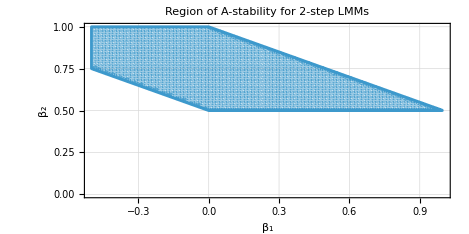

```mathematica
plt1=RegionPlot[a&&b/.κ->1,{β1,-1/2,1},{β2,0,1},GridLines->Automatic,AspectRatio->1/2,Frame->True,FrameLabel->{Subscript[β, 1], Subscript[β, 2]},RotateLabel->False,PlotLabel->"Region of A-stability for 2-step LMMs",PlotPoints->100,MaxRecursion->4]
```

```mathematica
{{-1/2,3/2}}
```

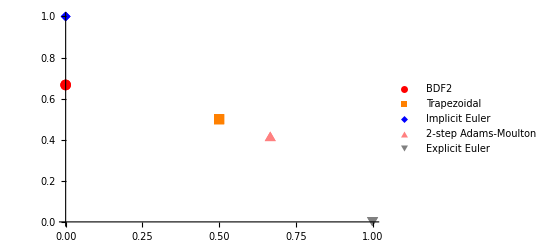

```mathematica
plt2=ListPlot[{{{0,2/3}},{{1/2,1/2}},{{0,1}},{{2/3,5/12}},{{1,0}}},PlotLegends->{"BDF2","Trapezoidal","Implicit Euler","2-step Adams-Moulton","Explicit Euler"},PlotStyle->{Red,Orange,Blue,Pink,Gray,Black},PlotMarkers->Automatic]
```

#### IMPORTANT: plt4 comes from k_to_c_coeffs.nb

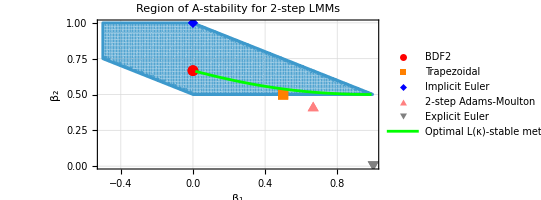

```mathematica
plt3=Show[plt1,plt2,plt4]
```

```mathematica
SetDirectory["C:\\Users\\Tyler Jensen\\Downloads"]
```

C:\Users\Tyler Jensen\Downloads

```mathematica
Export["perito_optimal_2step_astable.pdf",plt3]
```

perito_optimal_2step_astable.pdf

#### Ensuring no common roots (now no longer necessary for the paper)

```mathematica
Solve[Resultant[ρ[{3-2 Subscript[β, 1]-4 Subscript[β, 2],-4+2 Subscript[β, 1]+4 Subscript[β, 2],1}][ζ],σ[{-2+Subscript[β, 1]+3 Subscript[β, 2],Subscript[β, 1],Subscript[β, 2]}][ζ],ζ]==0,Subscript[β, 1]]
```

{{β_1→1-2 β_2},{β_1→1-2 β_2},{β_1→1-2 β_2}}

```mathematica
-2+2 Subscript[β, 1]+4 Subscript[β, 2]!=0//Simplify
```

β_1+2 β_2≠1

### Let’s see how it compares to BDF-like method conditions

```mathematica
astablecond/.{β0->0,β1->0}
```

(-2+β2) β2≤0&&(2-3 β2) β2≤0&&β2^2≥0&&β2≠0

```mathematica
Reduce[(-2+β2) β2≤0&&(2-3 β2) β2≤0&&β2^2≥0&&β2≠0]
```

2/3≤β2≤2

#### This matches what was found for BDF-like methods (also, 2/3 corresponds to BDF2)